```mathematica
Show[jupiterGraph,saturnGraph,uranusGraph,neptuneGraph,plutoGraph]
```

-Graphics3D-

```mathematica
(*Jupiter*)
jupSemiMajor=QuantityMagnitude[jupiterSemiMajorAxis,"Meters"];
jupSemiMinor = QuantityMagnitude[jupiterSemiMinorAxis,"Meters"];
paraJupx [t_]= jupSemiMajor*Cos[t];
paraJupy[t_]=jupSemiMinor*Sin[t];
jupParaPair = {paraJupx[t],paraJupy[t]};
jupPlot2D=ParametricPlot[jupParaPair,{t,0,2Pi}];
```

```mathematica
(*Saturn*)
```

```mathematica
satSemiMajor=QuantityMagnitude[saturnSemiMajorAxis,"Meters"];
satSemiMinor = QuantityMagnitude[saturnSemiMinorAxis,"Meters"];
paraSatx [t_]= satSemiMajor*Cos[t];
paraSaty[t_]=satSemiMinor*Sin[t];
satParaPair={paraSatx[t],paraSaty[t]};
satPlot2D=ParametricPlot[satParaPair,{t,0,2Pi}];
```

```mathematica
(*Uranus*)
```

```mathematica
uraSemiMajor=QuantityMagnitude[uranusSemiMajorAxis,"Meters"];
uraSemiMinor = QuantityMagnitude[uranusSemiMinorAxis,"Meters"];
paraUrax [t_]= uraSemiMajor*Cos[t];
paraUray[t_]= uraSemiMinor*Sin[t];
uraParaPair={paraUrax[t],paraUray[t]};
uraPlot2D=ParametricPlot[uraParaPair,{t,0,2Pi}];
```

```mathematica
(*Neptune*)
```

```mathematica
nepSemiMajor=QuantityMagnitude[neptuneSemiMajorAxis,"Meters"];
nepSemiMinor = QuantityMagnitude[neptuneSemiMinorAxis,"Meters"];
paraNepx [t_]= nepSemiMajor*Cos[t];
paraNepy[t_]=nepSemiMinor*Sin[t];
nepParaPair={paraNepx[t],paraNepy[t]};
nepPlot2D=ParametricPlot[nepParaPair,{t,0,2Pi}];
```

```mathematica
(*Pluto*)
```

```mathematica
pluSemiMajor=QuantityMagnitude[plutoSemiMajorAxis,"Meters"];
pluSemiMinor = QuantityMagnitude[plutoSemiMinorAxis,"Meters"];
paraPlux [t_]= pluSemiMajor*Cos[t];
paraPluy[t_]=pluSemiMinor*Sin[t];
pluParaPair={paraPlux[t],paraPluy[t]};
pluPlot2D=ParametricPlot[pluParaPair,{t,0,2Pi}];
```

```mathematica
outerPlanet2DParametrics={jupParaPair,satParaPair,uraParaPair,nepParaPair,pluParaPair};
```

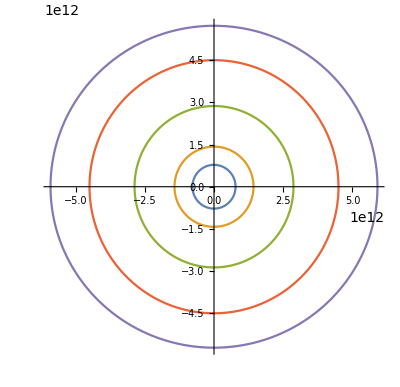

```mathematica
outerPlanet2DParaPlot=ParametricPlot[outerPlanet2DParametrics,{t,0,2Pi},PlotRange->All]
```

```mathematica
Animate[Show[outerPlanet2DParaPlot,Graphics[{PointSize[Large],Point[{paraJupx[t],paraJupy[t]}],Point[{paraSatx[t],paraSaty[t]}],Point[{paraUrax[t],paraUray[t]}],Point[{paraNepx[t],paraNepy[t]}],Point[{paraPlux[t],paraPluy[t]}]}]],{t,0,2Pi}]
```